```mathematica
D[Log[1-x^2], x]
D[1/Sqrt[1-x^2], x]
```

-(2 x)/(1-x^2)

x/((1-x^2)^(3/2))

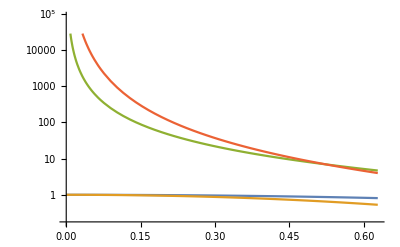

```mathematica
LogPlot[{Cos[x], Cos[x]^3, (2Cos[ x])/(1-Cos[x]^2), Cos[x]/((1-Cos[x]^2)^(3/2))}, {x, 0, Pi/5}]
```

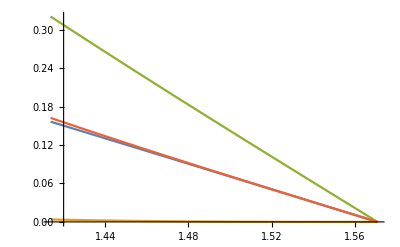

```mathematica
Plot[{Cos[x], Cos[x]^3, (2Cos[ x])/(1-Cos[x]^2), Cos[x]/((1-Cos[x]^2)^(3/2))}, {x, Pi/2-Pi/20, Pi/2}]
```

128

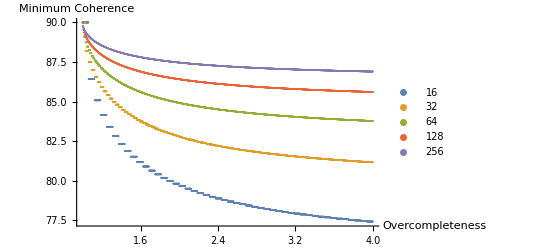

```mathematica
n = 128
ListPlot[Table[{oc, ArcCos[Sqrt[(IntegerPart[oc*2^sn]-2^sn)/(2^sn(IntegerPart[oc*2^sn]-1))]]*180/Pi}, {sn, 4, 8},{oc, 1, 4, .001}], PlotLegends->{16, 32, 64, 128, 256},AxesLabel->{"Overcompleteness", "Minimum Coherence"}]
```